```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
(*this is the length of the one-dimensional mesh[1]*)
L1=1.2444414542953002;
r=0.2;
cr={0.45,0.55};
NN=13;
Δθ=2π/NN;
Δl=2 r Sin[Δθ/2];
```

```mathematica
tabr=Table[cr +r{Cos[n Δθ],Sin[n Δθ]},{n,0,NN}];
```

```mathematica
tabr
```

{{0.65,0.55},{0.627091,0.642945},{0.563613,0.714597},{0.474107,0.748542},{0.379079,0.737003},{0.300298,0.682625},{0.255812,0.597863},{0.255812,0.502137},{0.300298,0.417375},{0.379079,0.362997},{0.474107,0.351458},{0.563613,0.385403},{0.627091,0.457055},{0.65,0.55}}

```mathematica
(*1 check transfer for scalar*)
```

```mathematica
(*test case 1*)
```

```mathematica
u2d[x_]:=1+x[[1]]^2 + 2 x[[2]]^2
```

```mathematica
plot2d={};
For[i=1,i<=NN,i++,
AppendTo[plot2d,Plot[u2d[tabr[[i]]+(s-(i-1)Δl)/Δl *(tabr[[i+1]]-tabr[[i]])],{s,(i-1)Δl,i Δl}]];
]
```

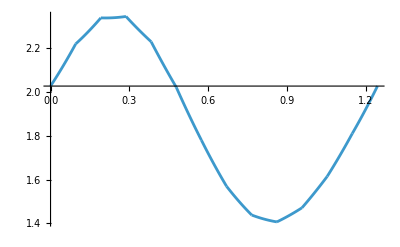

```mathematica
plot2d=Show[plot2d,PlotRange->Full]
```

```mathematica
tline=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_line.csv"][[2;;]];
tline=Table[{tline[[i,2]],tline[[i,1]]},{i,2,Length[tline]}]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_line.csv not found during Import.

Part::take: Cannot take positions 2 through -1 in $Failed.

{{All,2}}

```mathematica
plottline=ListPlot[tline,PlotStyle->{Red,PointSize->0.01}]
```

-Graphics-

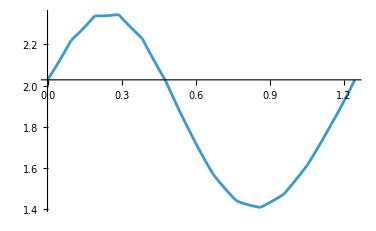

```mathematica
Show[plot2d,plottline]
```

```mathematica
(*2 check transfer for vector*)
```

```mathematica
(*test case 1*)
```

```mathematica
v2d[x_]:={1-x[[1]] + 2 x[[2]]^2,1-4x[[1]]^2 + 2 x[[2]]^2}
```

```mathematica
component=2;
```

```mathematica
plot2d={};
For[i=1,i<=NN,i++,
AppendTo[plot2d,Plot[v2d[tabr[[i]]+(s-(i-1)Δl)/Δl *(tabr[[i+1]]-tabr[[i]])][[component]],{s,(i-1)Δl,i Δl}]];
]
```

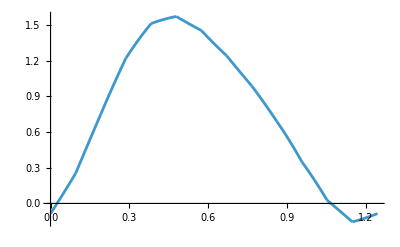

```mathematica
plot2d=Show[plot2d,PlotRange->Full]
```

```mathematica
tline=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/v_line.csv"][[2;;]];
tline=Table[{tline[[i,4]],tline[[i,component]]},{i,2,Length[tline]}]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/v_line.csv not found during Import.

Part::take: Cannot take positions 2 through -1 in $Failed.

Part::partw: Part 4 of 2;;All does not exist.

{{$Failed⟦2;;All⟧⟦2,4⟧,All}}

```mathematica
plottline=ListPlot[tline,PlotStyle->{Red,PointSize->0.01}]
```

-Graphics-

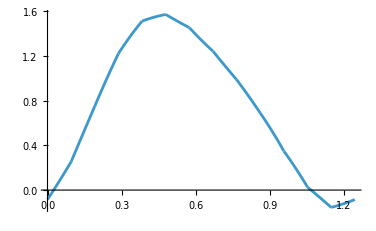

```mathematica
Show[plot2d,plottline]
```

```mathematica
(*3 check transfer for tensor*)
```

```mathematica
(*test case 1*)
```

```mathematica
t2d[x_]:={{Cos[2π (x[[1]]*x[[2]])],Sin[2 π x[[1]]]-Sin[2 π x[[2]]],(Sin[2 π x[[1]]]-Sin[2 π x[[2]]])^2},{Cos[2 π x[[1]]]^2-Sin[2 π x[[2]]],Cos[2π x[[1]]]^3-Sin[2 π (x[[1]]+x[[2]])],(Cos[2π x[[1]]]^3-Sin[2 π (x[[1]]+x[[2]])])^2}}
```

```mathematica
plotexact=Plot3D[t2d[{x,y}][[2,3]],{x,0,L},{y,0,h}]
```

-Graphics3D-

```mathematica
tline=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/nodal_values/t_2d.csv"][[2;;]];
tline=Table[{tline[[i,7]],tline[[i,8]],tline[[i,6]]},{i,2,Length[tline]}]
```

{{0.255812,0.597863,0.632315},{0.353021,0.637298,0.0251239},{0.379079,0.737003,1.09719},{0.341587,0.553747,0.202556},{0.255812,0.502137,0.997411},{0.404764,0.592076,0.296169},{0.436586,0.660476,1.83785},{0.474107,0.748542,3.7876},{0.362864,0.462772,0.375836},{0.300298,0.417375,0.901402},{0.415471,0.51941,0.0591552},{0.472624,0.567857,1.45925},{0.5333,0.623797,3.13433},{0.563613,0.714597,3.11884},{0.501901,0.686853,3.71199},{0.379079,0.362997,0.381541},{0.43749,0.433413,0.00402581},{0.491712,0.486346,0.737039},{0.558053,0.523367,1.70273},{0.592111,0.585027,2.2014},{0.627091,0.642945,1.77368},{0.474107,0.351458,0.00511502},{0.50119,0.415023,0.247457},{0.558053,0.454273,0.796916},{0.627091,0.457055,0.712554},{0.65,0.55,1.33202},{0.563613,0.385403,0.217903}}

```mathematica
error =Max[ Table[Abs[tline[[i,3]]-t2d[{tline[[i,1]],tline[[i,2]]}][[2,3]]],{i,1,Length[tline]}]]
```

2.22045×10^-15

```mathematica
plottline=ListPointPlot3D[tline,PlotStyle->{Red,PointSize->0.01}]
```

-Graphics3D-

```mathematica
Show[plotexact,plottline]
```

-Graphics3D-